```mathematica
Mathematica Project: Analysis of Kiva Loans
```

-Graphics-

## Insights from Loans disbursed by Kiva

Kiva is a non-profit organization that allows people to lend money via the internet to  low-income entrepreneurs. Kiva works with more than 300 microfinance institutions, social impact businesses, schools and non-profit organizations around the world, called “Field Partners” that post profiles of qualified local entrepreneurs on the Kiva website. Lenders browse borrower profiles on kiva.org and choose an entrepreneur they wish to fund. Lenders can loan money in increments as small as $25.

With the help of the Mathematica software, we will perform the analysis of ‘Kiva Loans’  data. The dataset is obtained from Kaggle and has more than 6 lakhs rows. We will use Mathematica for Exploratory Data Analysis. We will also apply Machine learning techniques such as Random Forests, Logistic Regression etc. for further analysis.

```mathematica
csvdata= Import["/Users/vipinragashetti/Vipin/Workspace/UCD/semester-I/Mathematica for Research/Project/myproject/kiva_loans.csv"];
```

```mathematica
header=csvdata[[1]];
data=csvdata[[2;;]];
kivaloan=Thread[header->#]&/@data//Map[Association]//Dataset
```

Dataset[<>]

The dataset used for this project is released by Kiva which provides loans to low-income entrepreneurs and students. The dataset  contains various variables listed below.

id			-  a unique identifier for each loan sanctioned.

funded_amount	-   amount that has been disbursed by Kiva to the field agent.

loan_amount		-  amount that has been released to the borrower by the field agent.

activity			-  low level category for which the loan has been issued.

sector			- high level category for which the loan has been issued.

use			- amount for which loan has been issued

country_code		- ISO country code of country in which loan was disbursed

country			-  Full country name of country in which loan was disbursed

region			-  Full region name within the country

currency		- The currency in which the loan was disbursed

partner_id		-  ID of partner organization

posted_time 		-  the time at which the loan is posted on Kiva by the field agent

disbursed_time		-  The time at which the loan is disbursed by the field agent to the borrower

funded_time 		-  The time at which the loan posted to Kiva gets funded by lenders completely

term_in_months	-  The duration for which the loan was disbursed in months

lender_count		-  The total number of lenders that contributed to this loan

repayment_status	- categorial variable for repayment status of the sanctioned loan.

## Exploratory Data Analy_sis

```mathematica
Dimensions[kivaloan]
```

{671205,20}

The kivaloan dataset has 6,71205 rows and 20 columns.

Check if there are any duplicate ids in kivaloan dataset

```mathematica
DuplicateFreeQ[kivaloan[[All,1]]]
```

True

There are no duplicate id entries in table.

Pie chart: Sector for which highest loan amount was disbursed

```mathematica
PieChart[Sort[Counts[kivaloan[All, "sector"]], Greater][1;;5], ChartStyle->"DarkRainbow", ChartLabels->Automatic, ChartLegends->Automatic, PlotLabel->Style["Top 5 Sectors where highest loan amount was disbursed", FontSize->13.5], ImageSize->Large]
```

-Graphics-

Finding the highest number of lender count in the dataset

```mathematica
Sort[kivaloan[All,"lender_count" ], Greater][1;;1]
```

Dataset[<>]

The highest number of lender count in the dataset is 2986.

Bar Chart:  Average loan amount disbursed among countries

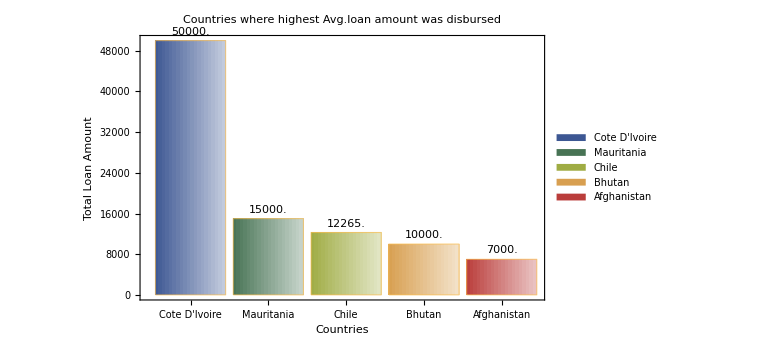

```mathematica
BarChart[Sort[kivaloan[GroupBy["country"], Mean, "loan_amount"], Greater][1;;5], 
ChartStyle->"DarkRainbow", ChartLabels->Automatic, ChartLegends->Automatic, ChartElementFunction->"FadingRectangle", PlotLabel->Style["Countries where highest Avg.loan amount was disbursed",FontSize->13.5], LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&),FrameLabel->{{"Total Loan Amount",None},{"Countries",None}},Frame->{{True,None},{True,None}}, ImageSize->Large]
```

Bar Chart: Repayment Interval vs Count

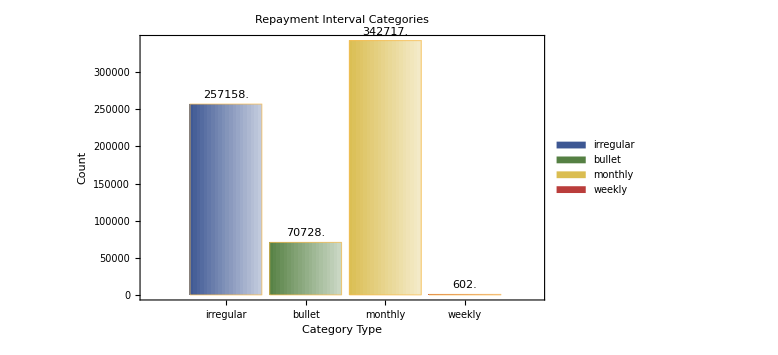

```mathematica
BarChart[Counts[kivaloan[All,"repayment_interval"]],ChartLabels-> Automatic,ChartStyle->"DarkRainbow",ChartLegends->Automatic, ChartElementFunction->"FadingRectangle", PlotLabel->Style["Repayment Interval Categories",FontSize->13.5], LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&),FrameLabel->{{"Count",None},{"Category Type",None}},Frame->{{True,None},{True,None}}, ImageSize->Large]
```

Top 5 Countries where highest total loan amount was disbursed

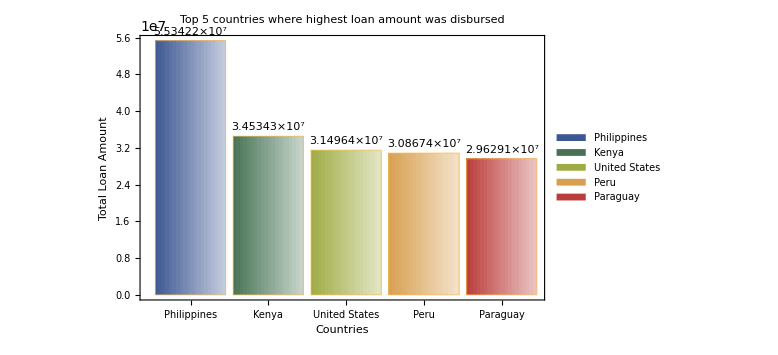

```mathematica
BarChart[Sort[kivaloan[GroupBy["country"], Total, "loan_amount"], Greater][1;;5], 
ChartStyle->"DarkRainbow", ChartLabels->Automatic, ChartLegends->Automatic, ChartElementFunction->"FadingRectangle", PlotLabel->Style["Top 5 countries where highest loan amount was disbursed",FontSize->13.5], LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&),FrameLabel->{{"Total Loan Amount",None},{"Countries",None}},Frame->{{True,None},{True,None}}, ImageSize->Large]
```

Countries where lowest loan amount was disbursed

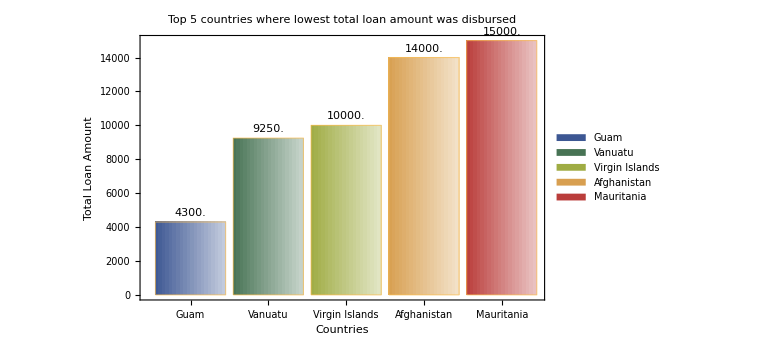

```mathematica
BarChart[Sort[kivaloan[GroupBy["country"], Total, "loan_amount"]][1;;5], 
ChartStyle->"DarkRainbow", ChartLabels->Automatic, ChartLegends->Automatic, ChartElementFunction->"FadingRectangle", PlotLabel->Style["Top 5 countries where lowest total loan amount was disbursed",FontSize->13.5], LabelingFunction->(Placed[Panel[NumberForm[N@#1]],Above]&),FrameLabel->{{"Total Loan Amount",None},{"Countries",None}},Frame->{{True,None},{True,None}}, ImageSize->Large]
```

WordCloud generates the word cloud graphics with different sizes based on the multiplicity in given input data

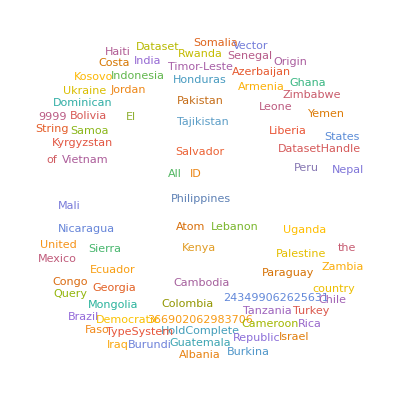

```mathematica
WordCloud[WordCounts[ToString[kivaloan[All,"country"]]]]
```

Country where highest number of loans/funds raised by Kiva was granted to Philippines followed by Kenya.

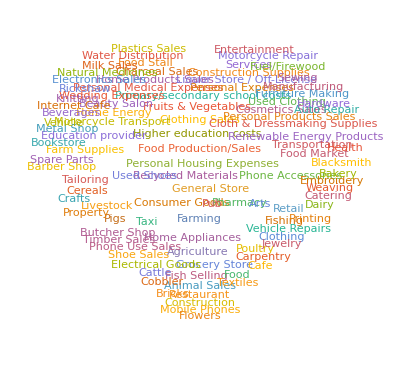

```mathematica
WordCloud[kivaloan[All,"activity"],-Graphics-]
```

Top Activities/Reason for which the loan was granted are General Store, Housing Expenses, Farming.

```mathematica
gender = kivaloan[All, "borrower_genders"];
Total[StringCount[Normal[gender],"male"]];
Total[StringCount[Normal[gender],"female"]];
PieChart3D[{Total[StringCount[Normal[gender],"male"]], Total[StringCount[Normal[gender],"female"]]}, ChartStyle->"DarkRainbow", ChartLabels->Placed[{"Male", "Female"},"RadialOuter"]]
```

-Graphics3D-

There are total of 13,46,212 individual male borrowers and 10,71,308 female borrowers.

## Machine Learning - Classification Predicting Labelled Data

Dividing the dataset into train and test dataset. We will use train dataset to build the model and then test the model with test data.

```mathematica
kivaloan = kivaloan[1;;400000];
train ={};
test = {};
For[i=1,i≤Length[kivaloan],i++,If[RandomInteger[{1,Length[kivaloan]}]<Length[kivaloan] 70/100,AppendTo[train,Normal[kivaloan[i,All]]],AppendTo[test,Normal[kivaloan[i,All]]]]]
train = Dataset[train];
test =Dataset[test];
```

Dropping the columns that will not be included in model

```mathematica
train = Dataset[Drop[train[1;;Length[train], Range[1,19]]]];
test = Dataset[Drop[test[1;;Length[test], Range[1,19]]]];
```

```mathematica
Clear[trainsetFeatures, testsetFeatures]
train = Drop[train[1;;Length[train], Range[1,19]]];
trainsetFeatures=train[1;;Length[train]];
trainsetFinal=Flatten[Normal@trainsetFeatures[1;;Length[train],{Most@#->Last@#}&],1];
testsetFeatures=test[1;;Length[test]];
testsetFinal=Flatten[Normal@testsetFeatures[1;;Length[test],{Most@#->Last@#}&],1];
```

#### Random Forest

```mathematica
Clear[classifierMeasurements, algoRandomForest]
algoRandomForest=Classify[trainsetFinal,Method->"RandomForest"]
ClassifierInformation[algoRandomForest]
classifierMeasurements= ClassifierMeasurements[algoRandomForest,testsetFinal]
classifierMeasurements/@{"Accuracy","Error"}//TableForm
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 18)
Classes | ,,bulletirregularmonthly
Accuracy | (91.4.) %
Method | RandomForest
Single evaluation time | 15.9 ms/example
Batch evaluation speed | 1.74 examples/ms
Loss | 0.613 ± 0.037
Model memory | 686. kB
Training examples used | 694 examples
Training time | 1.15 s
 |

ClassifierMeasurementsObject[…]

0.908497
0.0915033

The accuracy of the Random Forest Model is 91% and error produced by the model is 0.09%

Now lets plot the Accuracy Rejection Model

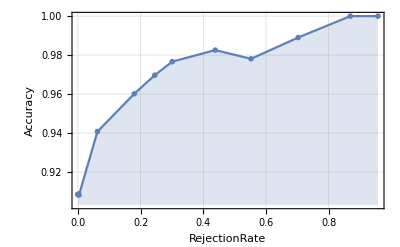

```mathematica
classifierMeasurements["AccuracyRejectionPlot"]
```

Classifying the labelled data. We are here trying to classify the repayment interval. The repayment interval can be of different types: Weekly, bullet, Irregular, monthly.

```mathematica
algoRandomForest[<|"id"->653051,"funded_amount"->300.,"loan_amount"->300.,"activity"->"Fruits & Vegetables","sector"->"Food","use"->"To buy seasonal, fresh fruits to sell. ","country_code"->"PK","country"->"Pakistan","region"->"Lahore","currency"->"PKR","partner_id"->247.,"posted_time"->"2014-01-01 06:12:39+00:00","disbursed_time"->"2013-12-17 08:00:00+00:00","funded_time"->"2014-01-02 10:06:32+00:00","term_in_months"->12.,"lender_count"->12,"tags"->"","borrower_genders"->"female"|>]
```

irregular

The repayment interval classified above is “Irregular” for the given user input for built Random Forest model.

#### Logistic Regression

```mathematica
Clear[classifierMeasurements, algoLogisticRegression]
algoLogisticRegression=Classify[trainsetFinal,Method->"LogisticRegression"]
ClassifierInformation[algoLogisticRegression]
classifierMeasurements= ClassifierMeasurements[algoLogisticRegression,testsetFinal]
classifierMeasurements/@{"Accuracy","Error"}//TableForm
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 18)
Classes | ,,bulletirregularmonthly
Accuracy | (94.42.9) %
Method | LogisticRegression
Single evaluation time | 16.9 ms/example
Batch evaluation speed | 1.62 examples/ms
Loss | 0.264 ± 0.046
Model memory | 666. kB
Training examples used | 694 examples
Training time | 3.13 s
 |

ClassifierMeasurementsObject[…]

0.931373
0.0686275

The accuracy of the Random Forest Model is 93% and error produced by the model is 0.06%

Now lets plot the Accuracy Rejection Model

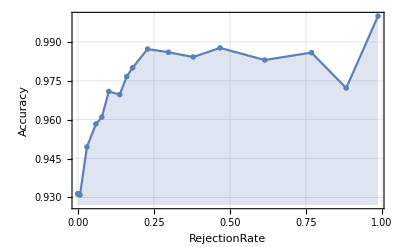

```mathematica
classifierMeasurements["AccuracyRejectionPlot"]
```

Classifying the labelled data on the trained Logistic Regression model.

```mathematica
algoLogisticRegression[<|"id"->653089,"funded_amount"->400.,"loan_amount"->400.,"activity"->"General Store","sector"->"Retail","use"->"to buy stock of rice, sugar and flour .","country_code"->"PK","country"->"Pakistan","region"->"Faisalabad","currency"->"PKR","partner_id"->245.,"posted_time"->"2014-01-01 12:04:57+00:00","disbursed_time"->"2013-12-24 08:00:00+00:00","funded_time"->"2014-01-08 00:35:14+00:00","term_in_months"->14.,"lender_count"->16,"tags"->"#Repeat Borrower, #Woman Owned Biz","borrower_genders"->"female"|>]
```

monthly

#### Neural Network

```mathematica
Clear[algoNeuralNetwork, classifierMeasurements]
algoNeuralNetwork=Classify[trainsetFinal,Method->"NeuralNetwork"]
ClassifierInformation[algoNeuralNetwork]
classifierMeasurements= ClassifierMeasurements[algoNeuralNetwork,testsetFinal]
classifierMeasurements/@{"Accuracy","Error"}//TableForm
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 18)
Classes | ,,bulletirregularmonthly
Accuracy | (53.5.) %
Method | NeuralNetwork
Single evaluation time | 21.2 ms/example
Batch evaluation speed | 961. examples/s
Loss | 0.959 ± 0.063
Model memory | 878. kB
Training examples used | 694 examples
Training time | 9.04 s
 |

ClassifierMeasurementsObject[…]

0.552288
0.447712

The accuracy of the Neural Network Model is 55% and error produced by the model is 44%. This is not the good model for kiva loan data as the accuracy is less.

Plot for the Accuracy Rejection Model

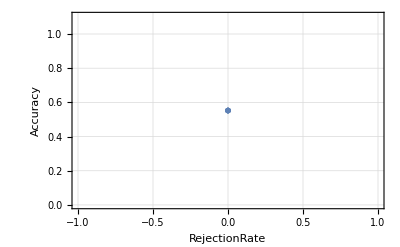

```mathematica
classifierMeasurements["AccuracyRejectionPlot"]
```

Classifying the labelled trained data on the Logistic Neural Network model.

```mathematica
algoNeuralNetwork[<|"id"->653089,"funded_amount"->400.,"loan_amount"->400.,"activity"->"General Store","sector"->"Retail","use"->"to buy stock of rice, sugar and flour .","country_code"->"PK","country"->"Pakistan","region"->"Faisalabad","currency"->"PKR","partner_id"->245.,"posted_time"->"2014-01-01 12:04:57+00:00","disbursed_time"->"2013-12-24 08:00:00+00:00","funded_time"->"2014-01-08 00:35:14+00:00","term_in_months"->14.,"lender_count"->16,"tags"->"#Repeat Borrower, #Woman Owned Biz","borrower_genders"->"female"|>]
```

monthly

#### Nearest Neighbors

```mathematica
Clear[classifierMeasurements, algoNearestNeighbors]
algoNearestNeighbors=Classify[trainsetFinal,Method->"NearestNeighbors"]
ClassifierInformation[algoNearestNeighbors]
classifierMeasurements= ClassifierMeasurements[algoNearestNeighbors,testsetFinal]
classifierMeasurements/@{"Accuracy","Error"}//TableForm
```

ClassifierFunction[…]

Classifier information
Data type | Mixed (number: 18)
Classes | ,,bulletirregularmonthly
Accuracy | (96.12.6) %
Method | NearestNeighbors
Single evaluation time | 13.4 ms/example
Batch evaluation speed | 2.07 examples/ms
Loss | 0.27 ± 0.045
Model memory | 7.09 MB
Training examples used | 694 examples
Training time | 975. ms
 |

ClassifierMeasurementsObject[…]

0.918301
0.0816993

The accuracy of the Nearest Neighbors Model is 92% and error produced by the model is 8%.

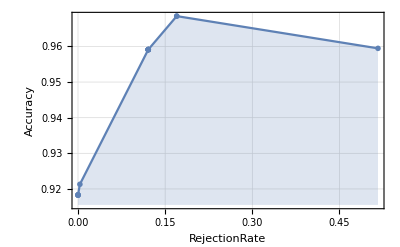

```mathematica
classifierMeasurements["AccuracyRejectionPlot"]
```

Classifying the labelled trained data on the Nearest Neighbors model.

```mathematica
algoNearestNeighbors[<|"id"->653208,"funded_amount"->500.,"loan_amount"->500.,"activity"->"Cereals","sector"->"Food","use"->"to buy cereals to increase his stock","country_code"->"KE","country"->"Kenya","region"->"Nanyuki","currency"->"KES","partner_id"->203.,"posted_time"->"2014-01-02 08:03:33+00:00","disbursed_time"->"2013-12-11 08:00:00+00:00","funded_time"->"2014-01-29 16:09:50+00:00","term_in_months"->14.,"lender_count"->20,"tags"->"#Elderly, #Repeat Borrower, user_favorite, user_favorite","borrower_genders"->"male"|>]
```

irregular

## Geographic Plotting

```mathematica
dhsmpi= Import["/Users/vipinragashetti/Vipin/Workspace/UCD/semester-I/Mathematica for Research/Project/myproject/dhs_mpi_loan.csv"];
header=dhsmpi[[1]];
data=dhsmpi[[2;;]];
dhsmpi=Thread[header->#]&/@data//Map[Association];
dhsmpi = Dataset[dhsmpi];
```

Converting the latitude and longitude from degrees to radians.

```mathematica
dhsmpi =dhsmpi[All,Append[#,"latradian"-> N[0.017*(#"lat"),5]]&];
dhsmpi =dhsmpi[All,Append[#,"lonradian"-> N[0.017*(#"lon"),5]]&];
dhsmpi =dhsmpi[All,Append[#,"latlon"-> {#"latradian",#"lonradian"}]&];
dhsmpi[[1;;]]
```

Dataset[<>]

Plotting the points on the Interactive map where the loans was distributed by Kiva

```mathematica
f[x_,y_]:=({x[[#]],y[[#]]})&/@Range[Min[Length[x],Length[y]]];
coord=f[dhsmpi[All,"lat"], dhsmpi[All,"lon"]];
```

```mathematica
DynamicGeoGraphics[{Orange,PointSize[Large],Point@GeoPosition@coord},GeoRange->"World",GeoProjection->"Robinson"]
```

Plotting the Interactive Map of Philippines where highest number of loans were distributed. [Map requires Internet connection to get loaded]

```mathematica
DynamicGeoGraphics[{Red,PointSize[Large],Point@GeoPosition@coord},GeoRange->Entity["Country", "Philippines"], GeoResolution->Quantity[1, "Kilometers"], GridLines->Automatic]
```

Plotting the Interactive map for Kenya where loans were distributed [Map requires Internet connection to get loaded]

```mathematica
DynamicGeoGraphics[{Blue,PointSize[Large],Point@GeoPosition@coord},GeoRange->Entity["Country", "Kenya"],GeoProjection->"Robinson", GeoGridLines->Automatic]
```

## Machine Learning - Prediction Predicting Unlabelled Data

In dhs_mpi_loan.csv, the countries are grouped into clusters and contains the geographic locations like latitude and longitude where the loan was disbursed. We will try to build the model using these geographic parameters and try to predict the cluster id. This data is provided my ‘The Demographic and Health Surveys Program’ (DHS) which is responsible for collecting and disseminating accurate, nationally representative data on health and population in developing countries .

We will be using the predict function which is used to predict/classify the unlabelled continuous data.

```mathematica
traindata = {};
For[i=1,i≤ Length[dhsmpi],i++,list = AppendTo[traindata,Normal[dhsmpi[i,"latlon"]]-> Normal[dhsmpi[i,"DHSCLUST"]]]]
```

#### Gaussian Process

```mathematica
predictGaussianProcess = Predict[traindata, Method-> "GaussianProcess"]
```

PredictorFunction[…]

```mathematica
Information[predictGaussianProcess]
```

Predictor information
Data type | NumericalVector (length: 2)
Standard deviation | 208. ± 13.
Method | GaussianProcess
Single evaluation time | 33.4 ms/example
Batch evaluation speed | 396. examples/s
Loss | 8.08 ± 0.86
Model memory | 222. MB
Training examples used | 5266 examples
Training time | 5 21
 |

Predicting the Cluster Id when the latitude is 4.19158 and longitude is -1.313 using Linear Regression model

```mathematica
predictGaussianProcess[{4.19158, -1.313}]
```

572.933

#### Linear Regression

```mathematica
predictLinearRegression =Predict[traindata,Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
Information[predictLinearRegression]
```

Predictor information
Data type | NumericalVector (length: 2)
Standard deviation | 383. ± 28.
Method | LinearRegression
Single evaluation time | 1.57 ms/example
Batch evaluation speed | 265. examples/ms
Loss | 7.42 ± 0.047
Model memory | 311. kB
Training examples used | 5266 examples
Training time | 4.26 s
 |

Predicting the Cluster Id when the latitude is 0.19058 and longitude is -1.30563 using Linear Regression model

```mathematica
predictLinearRegression[{0.19058, -1.30563}]
```

1395.44

#### Random Forest

```mathematica
predictRandomForest = Predict[traindata,Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
Information[predictRandomForest]
```

Predictor information
Data type | NumericalVector (length: 2)
Standard deviation | 236. ± 10.
Method | RandomForest
Single evaluation time | 3.78 ms/example
Batch evaluation speed | 36.2 examples/ms
Loss | 6.77 ± 0.05
Model memory | 437. kB
Training examples used | 5266 examples
Training time | 893. ms
 |

Predicting the Cluster Id when the latitude is 10.1801 and longitude is -1.401 using Random Forest model

```mathematica
predictRandomForest [{10.1801, -1.401}]
```

754.799

#### Nearest Neighbors

```mathematica
predictNearestNeighbors = Predict[traindata, Method->"NearestNeighbors"]
```

PredictorFunction[…]

```mathematica
Information[predictNearestNeighbors]
```

Predictor information
Data type | NumericalVector (length: 2)
Standard deviation | 175. ± 21.
Method | NearestNeighbors
Single evaluation time | 1.75 ms/example
Batch evaluation speed | 67.5 examples/ms
Loss | 5.13 ± 0.055
Model memory | 225. kB
Training examples used | 5266 examples
Training time | 763. ms
 |

Predicting the Cluster Id when the latitude is 11.1791 and longitude is -1.234 using  Nearest Neighbors model

```mathematica
predictNearestNeighbors[{11.1791, -1.234}]
```

291.

#### Neural Network

```mathematica
predictNeuralNetwork = Predict[traindata, Method->"NeuralNetwork"]
```

PredictorFunction[…]

```mathematica
Information[predictNeuralNetwork]
```

Predictor information
Data type | NumericalVector (length: 2)
Standard deviation | 198. ± 20.
Method | NeuralNetwork
Single evaluation time | 2.26 ms/example
Batch evaluation speed | 45.6 examples/ms
Loss | 6.7 ± 0.076
Model memory | 422. kB
Training examples used | 5266 examples
Training time | 1 26
 |

Predicting the Cluster Id when the latitude is 7.234 and longitude is -0.173 using  Nearest Neighbors model

```mathematica
predictNeuralNetwork[{7.234, -0.173}]
```

6329.1

## Conclusion

#### Exploratory Data Analysis Summary

The country where highest amount of kiva loans was disbursed is Philippines followed by Kenya and United States.

Large number of people are regular/monthly in the loan repayment. We also notice from the bar chart that there are significant people who are  irregular in repaying the loan.

Highest number of loans was disbursed for Agriculture sector followed by food and retail.

The country where lowest amount of loan was disbursed was Guam.

The country where with highest average loan amount is Cote D’Ivoire.

#### Machine Learning- Training, Classification and Prediction

Classification is used to classify the labelled data. Here were are trying to classify the repayment interval on the data. I have selected the first 4 lakhs records since mathematica software  was crashing intermittently and was taking more time to build models.

Here the data is divided into train and test subset and various Machine Learning techniques are applied  on the train data and  the model is tested using test data. We notice from the above models that Accuracy of classification is highest for Nearest Neighbors and Logistic Regression. These models are best models when you are trying to predict the labelled/discrete data. Neural Network performed bad for this dataset and is more suitable for very large and continuous type of response variable.

Prediction technique is used to predict unlabelled/continuous data. We  have used another dataset provided by DHS (Demographic and Health Surveys). Different countries together form a cluster and have a cluster id. We are trying to predict the cluster id when the latitude and longitude is provided as input to the model.

We have built the different models and predicted the cluster id from the trained model.

We have gained so many outcomes and insights from the Kiva crowd funded loan platform. Machine Learning and Exploratory Data Analysis can be performed in Mathematica software with ease. Machine Learning techniques like classification and prediction can be performed with a single command even though it takes some time for processing. 


In this project, I have learned how to analyse, build models, classify and predict the data in Mathematica, in addition to its computation capabilities. 

Mathematica is a user friendly application/software for Data Analysis and Machine Learning.